```mathematica
$Assumptions={Element[{ω, B, T},Reals]};
(* Just some pulse definitions *)
nhat = {0, 1, 0};
σ = {PauliMatrix[1], PauliMatrix[2], PauliMatrix[3]};
P4 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/4;
P8 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/8;
mP4 = MatrixExp[ⅈ*θ/2 * nhat.σ]/.θ->π/4;
P2 = MatrixExp[-ⅈ*θ/2 * nhat.σ]/.θ->π/2;
XSMALL = MatrixExp[-ⅈ* ϵ/2  * PauliMatrix[1]]

(* Setting T and B to unity, since they don't matter for this analysis *)
T = 1;
B = 1;
plus = 1/Sqrt[2] * {{1,1}};

(* Defining the free evolution unitary *)
Theta[t2_,t1_]:= Sin[ω*t2]/ω - Sin[ω*t1]/ω;
U[t2_, t1_] := MatrixExp[-ⅈ*B*PauliMatrix[3]*Theta[t2, t1]];
Dagger[X_] := Refine[Conjugate[Transpose[X]], {θ ∈ Reals, ω ∈ Reals}];

(* We'll assume everything is equally spaced, this is technically wlog since you can alwayas consider a longer sequence...*)
(* Produces the associated Z string unitary on the jth pulse*)
Zj[Ps_, j_] :=   Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[i=1,i<a + 1,i++,rtn=U[T/a*(i), T/a*(i-1)].list[[i]].rtn;
If[ i == j, rtn = PauliMatrix[3].rtn]];
rtn];

(* See the overleaf document. Strings with two Z's in them. *)
Vij[Ps_, i_, j_] := plus.Dagger[Zj[Ps, i]].Zj[Ps, j].Transpose[plus]//FullSimplify;

(* A Z expectation after j pulses, see the overleaf *)
Vj[Ps_, j_]:=  
Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
For[i=1,i<a + 1,i++,If[ i < j + 1, rtn=U[T/a*(i), T/a*(i-1)].list[[i]].rtn]];
plus.Dagger[rtn].PauliMatrix[3].rtn.Transpose[plus]]

(* See the overleaf document. Strings with two Z's in them. *)
Vij[Ps_, i_, j_] := plus.Dagger[Zj[Ps, i]].Zj[Ps, j].Transpose[plus]//FullSimplify;
```

{{Cos[ϵ/2],-ⅈ Sin[ϵ/2]},{-ⅈ Sin[ϵ/2],Cos[ϵ/2]}}

```mathematica
NullGen[i_]:=Null
CondEval[j_, vjs_, Ps_] := If[vjs[[j]]==Null, Vj[Ps, j], vjs[[j]]]
MatrixGen[Ps_] :=   Module[{list= Ps,a},a=Length[list];
Tij = ConstantArray[0,{a,a}];
Ti = ConstantArray[0, {a, 1}];
vjs = Array[NullGen, a];
For[j=1,j<a + 1,j++,
vjs[[j]] = CondEval[j,vjs, list][[1]][[1]]//FullSimplify;
Ti[[j]] = vjs[[j]]^2 * Theta[T/a *j, T/a *(j-1)]^2;
For[l=1,l<j ,l++,
vjs[[l]]=CondEval[l,vjs, list][[1]][[1]]//FullSimplify;
twopoint = Vij[list, l,j][[1]][[1]];
twoonepoint = 2*vjs[[l]]*vjs[[j]] ;
twotheta = Theta[T/a *l,(T/a)*(l-1)]*Theta[T/a *j, T/a*(j-1)];
Tij[[j]][[l]] = twotheta * (twopoint + Conjugate[twopoint]) - twoonepoint * twotheta]];
{Tij, Ti}]
```

```mathematica
Ps = {XSMALL,XSMALL};
MV = MatrixGen[Ps]//FullSimplify
M = MV[[1]];
V = MV[[2]];
```

{{{0,0},{(2 ⅇ^(-ⅈ (ϵ-Re[ϵ])) Cos[Re[ϵ]] Sin[ω/2] (-Sin[ω/2]+Sin[ω]))/ω^2,0}},{0,(ⅇ^(-2 ⅈ (ϵ-Re[ϵ])) (Sin[ω/2]-Sin[ω])^2 Sin[Re[ϵ]]^2 Sin[(2 Sin[ω/2])/ω]^2)/ω^2}}

```mathematica
M/.ϵ->0//MatrixForm
```

(0 | 0
(2 Sin[ω/2] (-Sin[ω/2]+Sin[ω]))/ω^2 | 0)

```mathematica
V/.ϵ->0//MatrixForm
```

(0
0)

```mathematica
maxω = 1000;
int = NIntegrate[M, {ω, 0, maxω}, AccuracyGoal->25,PrecisionGoal->25,WorkingPrecision->40,MaxRecursion->100000000,{Method->"QuasiMonteCarlo"}]
```

NIntegrate::inumr: The integrand (2 ⅇ^(-ⅈ (ϵ-Re[ϵ])) Cos[Re[ϵ]] Sin[ω/2] (-Sin[ω/2]+Sin[ω]))/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0,0},{NIntegrate[(2 ⅇ^(-ⅈ (ϵ-Re[ϵ])) Cos[Re[ϵ]] Sin[ω/2] (-Sin[ω/2]+Sin[ω]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}],0}}

```mathematica
int//MatrixForm
M /. ω->maxω//MatrixForm//N
```

NIntegrate::inumr: The integrand (2 ⅇ^(-ⅈ (ϵ-Re[ϵ])) Cos[Re[ϵ]] Sin[ω/2] (-Sin[ω/2]+Sin[ω]))/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

(0 | 0
NIntegrate[(2 ⅇ^(-ⅈ (ϵ-Re[ϵ])) Cos[Re[ϵ]] Sin[ω/2] (-Sin[ω/2]+Sin[ω]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}] | 0)

(0. | 0.
-1.2112×10^-6 2.71828^((0.-1. ⅈ) (ϵ-1. Re[ϵ])) Cos[Re[ϵ]] | 0.)

```mathematica
Total[int, 2]
```

NIntegrate::inumr: The integrand (2 (-1+2 Cos[(T ω)/5]) Sin[(T ω)/5]^2)/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (2 Sin[(T ω)/5] (-Sin[(2 T ω)/5]+Sin[(3 T ω)/5]))/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (2 (Sin[(T ω)/5]-Sin[(2 T ω)/5]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]))/ω^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[(2 (-1+2 Cos[(T ω)/5]) Sin[(T ω)/5]^2)/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 (-1+2 Cos[(3 T ω)/5]) (Sin[(T ω)/5]-Sin[(2 T ω)/5])^2)/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 (Sin[(T ω)/5]-Sin[(2 T ω)/5]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 Sin[(T ω)/5] (-Sin[(2 T ω)/5]+Sin[(3 T ω)/5]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 (Sin[(T ω)/5]-Sin[(2 T ω)/5]) (Sin[(3 T ω)/5]-Sin[(4 T ω)/5]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) (Sin[(3 T ω)/5]-Sin[(4 T ω)/5]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 Sin[(T ω)/5] (-Sin[(3 T ω)/5]+Sin[(4 T ω)/5]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) (Sin[(4 T ω)/5]-Sin[T ω]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 (Sin[(3 T ω)/5]-Sin[(4 T ω)/5]) (Sin[(4 T ω)/5]-Sin[T ω]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]+NIntegrate[(2 Sin[(T ω)/5] (-Sin[(4 T ω)/5]+Sin[T ω]))/ω^2,{ω,0,maxω},AccuracyGoal→25,PrecisionGoal→25,WorkingPrecision→40,MaxRecursion→100000000,{Method→QuasiMonteCarlo}]

```mathematica
IPs = {PauliMatrix[4], PauliMatrix[4]}; 
IMV = MatrixGen[IPs]/.T->1;
IM = IMV[[1]]
IV = IMV[[2]]
```

{{0,0},{(2 Sin[ω/2] (-Sin[ω/2]/ω+Sin[ω]/ω))/ω,0}}

{0,0}

```mathematica
maxω = 10000;
int = NIntegrate[IM, {ω, 0, maxω}, AccuracyGoal->5]
```

{{0.,0.},{0.0000999712,0.}}

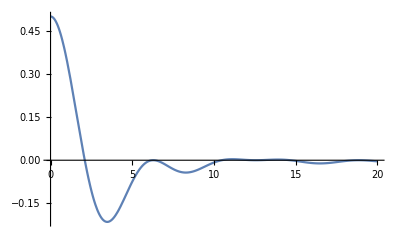

```mathematica
Plot[Total[IM, 2], {ω, 0 ,20}, PlotRange->All]
```

```mathematica
IV//MatrixForm
```

(0
0)

```mathematica
Total[IM, 1]//MatrixForm
```

((2 Sin[ω/2] (-Sin[ω/2]/ω+Sin[ω]/ω))/ω
0)

```mathematica
(*Not transposing might be correct, since the transposed matrix has an extra zero. Just pattern matching.*)
(* Also, perhaps unsurprising with this particular pulse sequence, but a lot of the terms are very close to each other.*)
 NIntegrate[(Total[M, 1] - V)/.T->1/.B->1, {ω, 0, maxω}, AccuracyGoal->25,PrecisionGoal->25,WorkingPrecision->40,MaxRecursion->100000000,{Method->"QuasiMonteCarlo"}]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -0.2652791695328652376367238851903097224644 and 0.009712660593031645667438954545863280552358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -0.2658008536480671342173644247425561631444 and 0.01007878589996714238173476297903661951401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -0.2692152349089411848461752500653958469268 and 0.009804146426060289463659903360440735329081 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0,-0.2652791695328652376367238851903097224644,-0.2658008536480671342173644247425561631444,-0.2692152349089411848461752500653958469268,-0.2935801647061539702401389549452252575636}

```mathematica
Ps = {PauliMatrix[4],P2,PauliMatrix[4],P2,PauliMatrix[4]};
MV = MatrixGen[Ps]//FullSimplify
M = MV[[1]];
V = MV[[2]];
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,(2 (Sin[(T ω)/5]-Sin[(2 T ω)/5]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) Sin[(2 B Sin[(T ω)/5])/ω]^2)/ω^2,0,0,0},{(2 Cos[(2 B (Sin[(T ω)/5]-Sin[(3 T ω)/5]))/ω] Sin[(T ω)/5] (Sin[(3 T ω)/5]-Sin[(4 T ω)/5]))/ω^2,(Cos[(2 B Sin[(T ω)/5])/ω] (Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(T ω)/5]-Sin[(2 T ω)/5]) (-Sin[(3 T ω)/5]+Sin[(4 T ω)/5]))/ω^2,(Cos[(2 B Sin[(T ω)/5])/ω] (Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) (-Sin[(3 T ω)/5]+Sin[(4 T ω)/5]))/ω^2,0,0},{(2 Cos[(2 B (Sin[(T ω)/5]-Sin[(3 T ω)/5]))/ω] Sin[(T ω)/5] (Sin[(4 T ω)/5]-Sin[T ω]))/ω^2,((-1+2 Cos[(3 T ω)/5]) Cos[(2 B Sin[(T ω)/5])/ω] (-Cos[(2 B Sin[(3 T ω)/5])/ω]+Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(T ω)/5]-Sin[(2 T ω)/5])^2)/ω^2,(Cos[(2 B Sin[(T ω)/5])/ω] (Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) (-Sin[(4 T ω)/5]+Sin[T ω]))/ω^2,-((-4+(Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω])^2) (Sin[(3 T ω)/5]-Sin[(4 T ω)/5]) (Sin[(4 T ω)/5]-Sin[T ω]))/(2 ω^2),0}},{0,(Cos[(2 B Sin[(T ω)/5])/ω]^2 (Sin[(T ω)/5]-Sin[(2 T ω)/5])^2)/ω^2,(Cos[(2 B Sin[(T ω)/5])/ω]^2 (Sin[(2 T ω)/5]-Sin[(3 T ω)/5])^2)/ω^2,((Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω])^2 (Sin[(3 T ω)/5]-Sin[(4 T ω)/5])^2)/(4 ω^2),((Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω])^2 (Sin[(4 T ω)/5]-Sin[T ω])^2)/(4 ω^2)}}

```mathematica
M//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | (2 (Sin[(T ω)/5]-Sin[(2 T ω)/5]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) Sin[(2 B Sin[(T ω)/5])/ω]^2)/ω^2 | 0 | 0 | 0
(2 Cos[(2 B (Sin[(T ω)/5]-Sin[(3 T ω)/5]))/ω] Sin[(T ω)/5] (Sin[(3 T ω)/5]-Sin[(4 T ω)/5]))/ω^2 | (Cos[(2 B Sin[(T ω)/5])/ω] (Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(T ω)/5]-Sin[(2 T ω)/5]) (-Sin[(3 T ω)/5]+Sin[(4 T ω)/5]))/ω^2 | (Cos[(2 B Sin[(T ω)/5])/ω] (Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) (-Sin[(3 T ω)/5]+Sin[(4 T ω)/5]))/ω^2 | 0 | 0
(2 Cos[(2 B (Sin[(T ω)/5]-Sin[(3 T ω)/5]))/ω] Sin[(T ω)/5] (Sin[(4 T ω)/5]-Sin[T ω]))/ω^2 | ((-1+2 Cos[(3 T ω)/5]) Cos[(2 B Sin[(T ω)/5])/ω] (-Cos[(2 B Sin[(3 T ω)/5])/ω]+Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(T ω)/5]-Sin[(2 T ω)/5])^2)/ω^2 | (Cos[(2 B Sin[(T ω)/5])/ω] (Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω]) (Sin[(2 T ω)/5]-Sin[(3 T ω)/5]) (-Sin[(4 T ω)/5]+Sin[T ω]))/ω^2 | -((-4+(Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω])^2) (Sin[(3 T ω)/5]-Sin[(4 T ω)/5]) (Sin[(4 T ω)/5]-Sin[T ω]))/(2 ω^2) | 0)

```mathematica
V//MatrixForm
```

(0
(Cos[(2 B Sin[(T ω)/5])/ω]^2 (Sin[(T ω)/5]-Sin[(2 T ω)/5])^2)/ω^2
(Cos[(2 B Sin[(T ω)/5])/ω]^2 (Sin[(2 T ω)/5]-Sin[(3 T ω)/5])^2)/ω^2
((Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω])^2 (Sin[(3 T ω)/5]-Sin[(4 T ω)/5])^2)/(4 ω^2)
((Cos[(2 B Sin[(3 T ω)/5])/ω]-Cos[(2 B (-2 Sin[(T ω)/5]+Sin[(3 T ω)/5]))/ω])^2 (Sin[(4 T ω)/5]-Sin[T ω])^2)/(4 ω^2))

```mathematica
NIntegrate[M/.T->1/.B->10, {ω, 0, maxω}, AccuracyGoal->25,PrecisionGoal->25,WorkingPrecision->40,MaxRecursion->100000000,{Method->"QuasiMonteCarlo"}]//MatrixForm
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -0.01790920724490885632578762291227775956259 and 0.038575304194721244288933170246052192895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -0.01412536970832968291499159374774038464781 and 0.04224751592751666111601808693677773250204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.1098899206978388095559063298842260487115 and 0.02365631808705617197455761834366299422166 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | -0.01790920724490885632578762291227775956259 | 0 | 0 | 0
-0.01412536970832968291499159374774038464781 | 0.1098899206978388095559063298842260487115 | 0.02861595729769043954404639322404410611165 | 0 | 0
-0.07419520929427989669799491151828927017349 | 0.04036143392321338522641640130632843902626 | 0.1040601409493718061701104182458101598486 | -0.01174669282888334044205889436334471048412 | 0)

```mathematica
XMatrixGen[Ps_] :=   Module[{list= Ps,a},a=Length[list];
X = ConstantArray[0,{a,a}];
For[j=1,j<a + 1,j++,
For[l=1,l<=j ,l++,
X[[j]][[l]] = Xij[j, l];]];
X]
```

```mathematica
Ps = {P8, P4,P8,P4 , P2,P2, P2,P2, P2,P2, P2,P2, P2,P2, P2,P2};
```

```mathematica
XMatrixGen[Ps]//MatrixForm
```

{}

```mathematica
T=1;
label[k_,x_]:=Graphics@Text["k = "<>ToString[k],{uh[x,a,go,s,m,k],x},{0,-1}];
Show[Table[Plot[Vj[Ps, a][[1]][[1]], {ω, 0, 1000}, PlotRange->All, PlotLabels->a],{a, Length[Ps] - 1, Length[Ps]}]]
```

-Graphics-

```mathematica
Vj[Ps, 5][[1]][[1]]//FullSimplify
```

-Cos[(B Sin[(T ω)/2])/ω]^2

```mathematica
T=.5;
Show[Table[Table[Plot[Re[Vij[Ps, a, b][[1]][[1]]], {ω, 0, 10}, PlotRange->All, PlotLabels->ToString[a]<>ToString[b]],{a, 0, 5}],{b, 15, 16}]]
```

-Graphics-

```mathematica
SeedRandom[137];
numsamples = 32;
results = Table[NIntegrate[Table[Abs[Theta[t1+1/n, t1]* Theta[t2+1/n, t2]], {t1, RandomReal[{0, 1}, numsamples]}, {t2,RandomReal[{0, 1}, numsamples]}],{ω, 0, 1000}], {n, {10, 20, 30, 40, 50}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {17.2671}. NIntegrate obtained 0.127092 and 0.00031801 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {3.93023}. NIntegrate obtained 0.126912 and 0.000253065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {35.6549}. NIntegrate obtained 0.137271 and 0.000518546 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{{0.127092,0.126912,0.137271,0.144761,0.13578,0.126601,0.126942,0.126747,0.126572,0.126419,0.126778,0.125255,0.125608,0.121136,0.126461,0.129439,0.123036,0.126843,0.126571,0.126542,0.125154,0.126,0.125746,0.127029,0.126677,0.127152,0.126264,0.148571,0.126346,0.126403,0.126625,0.121355},{0.127175,0.126803,0.126463,0.126541,0.151584,0.126957,0.126256,0.127608,0.126462,0.126755,0.132455,0.127755,0.126511,0.126555,0.126254,0.128492,0.12649,0.126463,0.126556,0.126346,0.126378,0.12666,0.126163,0.126561,0.125479,0.126807,0.126527,0.126633,0.12634,0.126305,0.126341,0.12646},{0.126759,0.126317,0.127341,0.126544,0.126835,0.126698,0.127059,0.126601,0.123232,0.151438,0.126759,0.126749,0.126599,0.126884,0.127233,0.12645,0.126332,0.126377,0.127099,0.127096,0.126518,0.126509,0.1267,0.126779,0.126888,0.126621,0.124883,0.126549,0.12333,0.124287,0.125926,0.126702},{0.126251,0.124891,0.128213,0.126103,0.127403,0.126096,0.126426,0.126154,0.127336,0.126127,0.154332,0.125248,0.127783,0.122016,0.125529,0.126034,0.126512,0.126434,0.126331,0.126369,0.126371,0.126513,0.127241,0.126577,0.126566,0.126229,0.126473,0.126165,0.126522,0.126408,0.126414,0.13961},{0.126966,0.123175,0.125779,0.126874,0.127572,0.126392,0.141485,0.126933,0.122218,0.126686,0.126727,0.126101,0.121354,0.124808,0.126588,0.130347,0.126542,0.126763,0.126576,0.126412,0.126516,0.124997,0.126292,0.126419,0.126869,0.139067,0.126814,0.128119,0.12685,0.12697,0.120377,0.122841},{0.125474,0.125724,0.123649,0.127178,0.1264,0.126609,0.125476,0.128593,0.126467,0.15555,0.122774,0.12667,0.126629,0.126617,0.128896,0.125893,0.128558,0.122094,0.126059,0.128269,0.126314,0.126679,0.125507,0.13521,0.126416,0.126547,0.126517,0.126937,0.126566,0.128957,0.134954,0.12636},{0.126494,0.146993,0.126698,0.126912,0.126639,0.126779,0.125739,0.12651,0.150274,0.126517,0.126703,0.126612,0.148061,0.126549,0.126874,0.126629,0.125555,0.125938,0.127314,0.126935,0.126694,0.125661,0.127563,0.126231,0.12763,0.126803,0.126037,0.126541,0.125701,0.126248,0.126327,0.126529},{0.12704,0.126996,0.126554,0.127234,0.126611,0.126995,0.125916,0.126541,0.126448,0.128969,0.153985,0.126863,0.149471,0.146419,0.122701,0.123788,0.126409,0.126577,0.126561,0.126529,0.128132,0.126515,0.126409,0.126545,0.126116,0.126169,0.127703,0.126934,0.126521,0.126721,0.126188,0.142795},{0.126549,0.126687,0.126506,0.130158,0.126523,0.127003,0.126707,0.138034,0.126794,0.126545,0.133386,0.127455,0.128088,0.12615,0.125574,0.127548,0.126594,0.126415,0.126029,0.127057,0.126551,0.126613,0.1266,0.122502,0.126618,0.126416,0.126734,0.126562,0.126346,0.126907,0.128141,0.126058},{0.125959,0.126997,0.146541,0.127622,0.125902,0.12666,0.127775,0.127929,0.126634,0.126578,0.126912,0.126538,0.12664,0.126147,0.152509,0.124991,0.126626,0.126422,0.126966,0.125945,0.144289,0.126369,0.124993,0.126302,0.126431,0.126544,0.12908,0.12662,0.126412,0.12632,0.126141,0.126463},{0.126163,0.126438,0.126662,0.125572,0.126591,0.126294,0.126384,0.12654,0.135617,0.126581,0.126364,0.126992,0.126363,0.126153,0.126246,0.126875,0.126743,0.126974,0.130073,0.126569,0.126286,0.126085,0.125625,0.133961,0.12462,0.134605,0.126399,0.1266,0.125507,0.126681,0.126439,0.126039},{0.125827,0.126509,0.126342,0.125856,0.130302,0.121602,0.125435,0.125133,0.126548,0.125882,0.13678,0.125254,0.126457,0.125046,0.126124,0.12612,0.126429,0.126656,0.12663,0.125836,0.125556,0.124834,0.125873,0.126493,0.1243,0.126495,0.134113,0.126513,0.126435,0.131453,0.125803,0.126674},{0.123742,0.126578,0.126056,0.126684,0.131087,0.125135,0.125914,0.126555,0.126558,0.125651,0.126589,0.126564,0.127054,0.126449,0.126393,0.12163,0.124361,0.126792,0.126966,0.126322,0.126145,0.124397,0.124127,0.126493,0.121495,0.127232,0.126987,0.12158,0.124957,0.126642,0.12589,0.126512},{0.12655,0.126772,0.126642,0.126849,0.124805,0.125081,0.126631,0.126933,0.126546,0.127687,0.139285,0.127356,0.126586,0.146209,0.126985,0.125364,0.127917,0.126283,0.126404,0.121201,0.125916,0.126669,0.126518,0.127794,0.126566,0.125977,0.12904,0.125949,0.126138,0.127134,0.127819,0.125026},{0.126595,0.126532,0.126272,0.125429,0.125761,0.126328,0.126197,0.129218,0.128075,0.125224,0.127067,0.127998,0.126268,0.122068,0.126646,0.126484,0.126282,0.142357,0.126127,0.129168,0.121406,0.121551,0.126364,0.126508,0.126421,0.125745,0.125671,0.126749,0.125785,0.125203,0.126502,0.125844},{0.125391,0.12667,0.128221,0.126492,0.126026,0.126906,0.126681,0.124741,0.127589,0.126726,0.12133,0.127432,0.125229,0.12518,0.128881,0.126859,0.12697,0.128179,0.126898,0.127738,0.139443,0.126173,0.126312,0.126491,0.126146,0.126706,0.125271,0.122942,0.126502,0.126809,0.125897,0.148789},{0.126481,0.126331,0.127211,0.126071,0.126522,0.140727,0.126767,0.126825,0.127749,0.127617,0.128948,0.129044,0.126204,0.139959,0.126476,0.126777,0.127007,0.126287,0.126542,0.12678,0.126736,0.127087,0.126491,0.146241,0.126608,0.12602,0.131994,0.126678,0.126432,0.126212,0.123166,0.126746},{0.125599,0.144983,0.126115,0.121885,0.126531,0.126351,0.126385,0.126741,0.126409,0.128254,0.126522,0.125257,0.127268,0.126423,0.128539,0.126736,0.127486,0.126659,0.126221,0.127041,0.127477,0.126543,0.127357,0.126599,0.126621,0.122251,0.125578,0.126196,0.125199,0.126871,0.12788,0.126178},{0.122526,0.126644,0.131154,0.126864,0.126299,0.126255,0.127239,0.124091,0.12617,0.126503,0.125916,0.154921,0.12702,0.127064,0.126499,0.126537,0.126833,0.126444,0.126247,0.125529,0.128534,0.123455,0.133462,0.124981,0.12655,0.127115,0.126304,0.126616,0.128309,0.125933,0.126638,0.126561},{0.125869,0.125603,0.126507,0.126869,0.126566,0.123115,0.135367,0.126049,0.1221,0.127263,0.12639,0.122972,0.141299,0.128157,0.140509,0.131899,0.126177,0.149697,0.122027,0.126303,0.125555,0.127708,0.126295,0.12648,0.127999,0.126864,0.123476,0.127367,0.12687,0.125696,0.137017,0.12639},{0.125458,0.126524,0.127124,0.126642,0.126563,0.12671,0.126071,0.128341,0.127946,0.126554,0.126644,0.126241,0.146605,0.126618,0.126542,0.126555,0.151226,0.126485,0.126291,0.126968,0.126395,0.1262,0.12632,0.126452,0.126113,0.126336,0.126645,0.124741,0.126722,0.126511,0.126742,0.126828},{0.125933,0.128721,0.126523,0.126566,0.126291,0.126339,0.125927,0.126438,0.122967,0.127069,0.126635,0.126538,0.156067,0.126312,0.126545,0.126529,0.12588,0.126814,0.126357,0.126783,0.126578,0.126042,0.126308,0.126879,0.138164,0.126565,0.126544,0.126745,0.155963,0.126328,0.126494,0.127443},{0.126014,0.125268,0.126757,0.134813,0.125844,0.125673,0.125181,0.125329,0.149172,0.125565,0.125424,0.126616,0.126964,0.126539,0.126061,0.121227,0.123164,0.126304,0.12672,0.12672,0.126419,0.127367,0.126722,0.128163,0.126161,0.126156,0.127296,0.12554,0.127181,0.126322,0.125622,0.127009},{0.126428,0.126107,0.125983,0.126578,0.12131,0.126321,0.125877,0.144022,0.126269,0.126707,0.126538,0.12655,0.126711,0.125919,0.127092,0.126584,0.126568,0.126168,0.124594,0.144204,0.125938,0.126485,0.127758,0.134027,0.126036,0.126504,0.125645,0.125278,0.124451,0.126297,0.126548,0.126714},{0.126374,0.123868,0.126648,0.126476,0.121539,0.127079,0.126269,0.126512,0.12658,0.124305,0.126422,0.126681,0.126265,0.126535,0.126642,0.143551,0.126405,0.129,0.123343,0.126891,0.125915,0.129391,0.126528,0.124001,0.123843,0.126611,0.12653,0.126496,0.126508,0.125638,0.126649,0.128178},{0.127397,0.126274,0.126654,0.126726,0.126442,0.127026,0.127362,0.130467,0.126815,0.127312,0.126748,0.1268,0.127061,0.126503,0.127344,0.128177,0.124496,0.126469,0.126853,0.126428,0.126433,0.126872,0.127083,0.12651,0.126599,0.126829,0.128176,0.131939,0.128289,0.126351,0.120965,0.126776},{0.126585,0.125952,0.126404,0.127059,0.132621,0.126374,0.126514,0.127041,0.126375,0.126653,0.126114,0.12607,0.126659,0.126112,0.126181,0.126494,0.126977,0.12626,0.127634,0.126387,0.126279,0.126321,0.126965,0.126702,0.126278,0.126012,0.126414,0.126287,0.12676,0.126542,0.126457,0.126491},{0.127741,0.121709,0.126498,0.126761,0.126212,0.126888,0.125794,0.127642,0.125174,0.125978,0.126027,0.12643,0.126891,0.155258,0.129315,0.124708,0.12453,0.127134,0.123223,0.122594,0.128054,0.126218,0.126626,0.126265,0.127198,0.13688,0.12639,0.12759,0.120423,0.126182,0.125937,0.126846},{0.126505,0.126492,0.126535,0.125042,0.13773,0.125943,0.126537,0.127085,0.135902,0.125496,0.136725,0.125381,0.146851,0.126637,0.123995,0.126815,0.126609,0.140645,0.144546,0.126647,0.124809,0.12666,0.121259,0.126406,0.126892,0.126565,0.12593,0.127937,0.155443,0.126505,0.12635,0.126944},{0.126418,0.12636,0.12669,0.1254,0.126538,0.1264,0.125612,0.144189,0.126966,0.126569,0.126384,0.127156,0.126394,0.128879,0.126353,0.12627,0.126439,0.125666,0.126811,0.128257,0.124597,0.127823,0.126227,0.126793,0.125625,0.1314,0.126164,0.126394,0.127225,0.125867,0.135231,0.125616},{0.126958,0.125665,0.126798,0.125981,0.124227,0.126412,0.126069,0.126764,0.126222,0.152295,0.126409,0.126973,0.126475,0.127195,0.126994,0.126414,0.126453,0.126569,0.13906,0.126454,0.12594,0.126435,0.126964,0.126432,0.12669,0.126618,0.126639,0.126175,0.126874,0.125899,0.12625,0.126517},{0.125791,0.124576,0.126415,0.126516,0.126754,0.126405,0.147362,0.148525,0.125942,0.146521,0.126429,0.126429,0.126279,0.126473,0.121717,0.126417,0.126433,0.126182,0.126075,0.12793,0.127447,0.126242,0.126635,0.124421,0.155244,0.126929,0.126861,0.126472,0.123583,0.125552,0.126646,0.126543}},{{0.0615661,0.0629582,0.0625376,0.0629636,0.0617768,0.0628424,0.0625437,0.0628244,0.0628548,0.0628671,0.0629324,0.0627841,0.0628122,0.0627489,0.0641423,0.0631263,0.0628801,0.0628752,0.059447,0.0637205,0.0628938,0.0628469,0.0603176,0.0628672,0.0628633,0.0629273,0.0628464,0.0629856,0.0628713,0.0627038,0.0624775,0.0626967},{0.0628143,0.0772917,0.062909,0.0630483,0.0630632,0.0629001,0.062938,0.0628656,0.0627841,0.0633474,0.0630013,0.06315,0.0646981,0.0628421,0.0614813,0.0628104,0.0630977,0.0630428,0.0632251,0.0631232,0.0633264,0.0621887,0.0629857,0.0630782,0.0628646,0.0629005,0.0627062,0.0629138,0.065962,0.0630903,0.0630824,0.0628722},{0.0612313,0.0629387,0.0629444,0.0631547,0.063131,0.0739418,0.0629854,0.0624814,0.0630588,0.0632284,0.0628842,0.0628424,0.0616791,0.0626048,0.062857,0.0627009,0.0628087,0.063249,0.0622651,0.0622973,0.0591692,0.0629143,0.0630375,0.0630153,0.0627782,0.0611802,0.0628546,0.0629998,0.0632777,0.0628907,0.0630816,0.0615722},{0.0626637,0.0630802,0.063003,0.0622837,0.0775343,0.0628991,0.0624973,0.0623297,0.0626918,0.0627206,0.0627893,0.0620639,0.0627353,0.0630432,0.0628776,0.0629486,0.0620423,0.0630607,0.0629729,0.0625213,0.0638575,0.0626446,0.0624118,0.0628033,0.0628218,0.0636952,0.063015,0.0624015,0.0627765,0.0628495,0.0772356,0.0629188},{0.0632363,0.0628575,0.0626362,0.0636649,0.0630349,0.0628672,0.0626104,0.0622628,0.063218,0.0631896,0.0593559,0.0637432,0.0627362,0.0618205,0.062841,0.0631452,0.0627273,0.0630286,0.0629033,0.0629507,0.0712879,0.0629581,0.0632238,0.0637298,0.0625687,0.0626694,0.0628764,0.0633724,0.0607205,0.0630641,0.0627397,0.0631339},{0.0628812,0.0628329,0.0630467,0.062547,0.0633127,0.0628889,0.0626963,0.0629403,0.0641754,0.0628412,0.0628226,0.0629227,0.062614,0.0628897,0.0630827,0.0630091,0.0628936,0.0629505,0.0626446,0.0631394,0.0628637,0.0631031,0.0629267,0.0629305,0.0671561,0.0629331,0.0629855,0.0629219,0.0628068,0.0630629,0.0634435,0.0628956},{0.0628745,0.0634725,0.0629575,0.0630493,0.0628948,0.0629381,0.0629945,0.0631834,0.0651093,0.0632306,0.0629614,0.0631677,0.0629494,0.0631031,0.0630485,0.0629188,0.062838,0.0628233,0.0630127,0.0629673,0.0629999,0.0634869,0.0638451,0.0630558,0.0630877,0.063871,0.062772,0.0629212,0.0633756,0.0625256,0.063066,0.0638127},{0.0631019,0.0626642,0.0628931,0.0604996,0.0629383,0.0627485,0.0632987,0.0624446,0.0604395,0.0632444,0.0628569,0.0619706,0.0629506,0.0627955,0.0628525,0.0628188,0.0633393,0.0628925,0.0630781,0.0613403,0.0630628,0.0630778,0.062751,0.0628569,0.0628344,0.0625194,0.0628203,0.0610404,0.0628251,0.0628837,0.0763967,0.0628174},{0.0626559,0.0625644,0.0630344,0.0625613,0.062944,0.0627774,0.0614635,0.0629302,0.0631736,0.0624328,0.062728,0.0633618,0.0624367,0.0728362,0.0634407,0.0629521,0.0630678,0.0631451,0.0634988,0.0649103,0.0634894,0.0638057,0.0635227,0.0629469,0.0627641,0.0624316,0.062778,0.0631736,0.0629177,0.063262,0.0604618,0.0594418},{0.0630461,0.0629057,0.0630235,0.0628814,0.0632209,0.0628465,0.0696084,0.0626781,0.0631135,0.0613358,0.0625916,0.0628705,0.0628529,0.0628571,0.0628732,0.0629084,0.0635457,0.0615738,0.0630316,0.0629993,0.0630255,0.0628481,0.0629905,0.0630977,0.062854,0.0628291,0.0750453,0.0625904,0.0635802,0.062933,0.062958,0.0629172},{0.0626613,0.0613741,0.0724011,0.0620546,0.0628819,0.0629298,0.0628053,0.0634916,0.0629332,0.0633244,0.0631319,0.0621093,0.0627998,0.063037,0.0628488,0.0625968,0.0628464,0.0627509,0.0628171,0.062905,0.0634467,0.0629366,0.0627532,0.0628403,0.0626687,0.063014,0.06293,0.0632666,0.0634611,0.0627653,0.0629285,0.0608099},{0.0628424,0.0627296,0.0630606,0.0628715,0.0773034,0.0631674,0.0632041,0.0628977,0.0629388,0.0631964,0.0627416,0.0657471,0.0628475,0.0627166,0.0623755,0.0634379,0.06307,0.0662114,0.0629741,0.0623176,0.0641652,0.06288,0.0669848,0.0628355,0.0625766,0.0624745,0.0629368,0.0632486,0.0709804,0.0626601,0.0607091,0.0634157},{0.0631043,0.060516,0.062795,0.0624214,0.0630928,0.0628553,0.0635668,0.0632615,0.0628313,0.0629815,0.0628635,0.062903,0.0611871,0.0629514,0.0628346,0.0631566,0.0630314,0.0628394,0.0628162,0.0629576,0.0627099,0.062787,0.0627597,0.062865,0.062929,0.062913,0.0629064,0.0629231,0.0630428,0.0628799,0.0629106,0.0628995},{0.0628639,0.0615038,0.0619911,0.0644566,0.0629211,0.0637886,0.0628823,0.0628646,0.073117,0.062672,0.0628469,0.0624671,0.0630571,0.0635375,0.0629268,0.0625948,0.063635,0.0619865,0.0637726,0.0626523,0.0629057,0.0629282,0.0630208,0.0635231,0.0628038,0.0628898,0.0628049,0.0629074,0.0627943,0.0628913,0.0628348,0.0620642},{0.0620595,0.0625858,0.0624255,0.0633282,0.0630694,0.0627736,0.0626483,0.0625221,0.0628217,0.0627263,0.0628245,0.0627837,0.0629701,0.0630876,0.0626761,0.0628242,0.0626629,0.0630679,0.0635555,0.0626423,0.0622787,0.0629973,0.0629285,0.0632322,0.0628532,0.0628056,0.0629384,0.0626726,0.0627604,0.0628703,0.063364,0.0618453},{0.0638164,0.0738909,0.0627705,0.0626549,0.062759,0.0628195,0.0775123,0.0628536,0.0628867,0.0628312,0.0628906,0.0774846,0.0630483,0.0627362,0.0629472,0.0628889,0.0639115,0.0627475,0.0629056,0.0628577,0.0630671,0.0629124,0.0629123,0.0628023,0.0628998,0.0629781,0.0629211,0.062364,0.0629038,0.063007,0.0620108,0.0754285},{0.0637928,0.0628658,0.0611691,0.0628524,0.0619344,0.0625922,0.0630188,0.0630357,0.062464,0.0629951,0.0626033,0.0628355,0.0628265,0.0627396,0.0624085,0.061549,0.0628483,0.0634825,0.0630191,0.0635664,0.0630963,0.0627586,0.0630958,0.0621154,0.0626209,0.0628743,0.0630166,0.0628763,0.0627885,0.0635092,0.0629521,0.0625702},{0.0628235,0.0628447,0.0628602,0.0633033,0.0630307,0.0634404,0.0634113,0.0630308,0.0628055,0.0628474,0.0632707,0.0629853,0.0626286,0.0631008,0.0628359,0.0658516,0.0633082,0.062759,0.063007,0.0572609,0.063073,0.0628541,0.0629573,0.0625243,0.0630278,0.0630132,0.0634296,0.0631505,0.0630566,0.0631187,0.0630191,0.0631946},{0.0628684,0.0626482,0.0627092,0.0571919,0.0629628,0.0628421,0.0628752,0.0632769,0.0630597,0.0629213,0.0629004,0.0631146,0.06233,0.0620737,0.0629251,0.0630489,0.063463,0.0628627,0.0629058,0.0629374,0.063068,0.062826,0.0634758,0.0630056,0.0623629,0.0625514,0.0628331,0.062954,0.0632291,0.0626466,0.0627811,0.0627826},{0.0628605,0.0629449,0.0624328,0.062933,0.0633668,0.0629521,0.0629726,0.061811,0.0628325,0.0629371,0.0629846,0.058371,0.0627825,0.0627585,0.0626607,0.0624707,0.0630385,0.0620349,0.0628338,0.0629043,0.0632967,0.0628432,0.0627103,0.0640257,0.0628277,0.0632329,0.0618119,0.0628172,0.06274,0.0628945,0.0628104,0.0632093},{0.0630341,0.0629354,0.0630272,0.0630369,0.0626473,0.0631181,0.0674115,0.0628259,0.063055,0.0618278,0.0629294,0.0626944,0.0634979,0.0628118,0.0676763,0.061644,0.0633838,0.0625458,0.0627941,0.0624683,0.0630903,0.0631194,0.0634827,0.0629367,0.062935,0.0630176,0.077519,0.0625536,0.062522,0.0628001,0.0625422,0.0617822},{0.0627737,0.0628929,0.0626112,0.0628806,0.0629138,0.0628435,0.0630487,0.0628182,0.062965,0.0624739,0.0759585,0.062815,0.0616642,0.0641134,0.0629803,0.0627886,0.0628902,0.0629843,0.0627596,0.0628619,0.0626595,0.061012,0.0628939,0.0630046,0.0631666,0.0624185,0.0626956,0.0625581,0.0615102,0.062941,0.0627649,0.0628438},{0.0629975,0.0628545,0.0627898,0.0626502,0.0635614,0.0628137,0.0623357,0.0617388,0.0633702,0.0626798,0.0633325,0.0632246,0.0633589,0.0630904,0.0624147,0.0630622,0.0626539,0.0610633,0.0629967,0.0625736,0.0621865,0.0629351,0.0630373,0.0627387,0.0628782,0.0627909,0.0622516,0.0631669,0.0627947,0.0619854,0.0628913,0.0630502},{0.0630207,0.062568,0.0625172,0.0626748,0.0631327,0.0628388,0.0630931,0.0628136,0.0622604,0.064876,0.0630714,0.0631484,0.0630086,0.0628632,0.062822,0.0627664,0.0587998,0.0625559,0.0627679,0.0627519,0.062663,0.0626853,0.0636043,0.0629479,0.0630045,0.0629377,0.0629171,0.0629327,0.0623181,0.0626901,0.0629374,0.0625892},{0.0630393,0.0620697,0.0632962,0.062263,0.0632116,0.0630262,0.0629666,0.0624199,0.0696765,0.0639409,0.0628336,0.0624654,0.0630556,0.0626144,0.0635192,0.0626705,0.0627003,0.0628695,0.0630811,0.0623669,0.0632344,0.0628919,0.0627438,0.0630274,0.0627682,0.0624039,0.0604458,0.0626033,0.0621395,0.0629638,0.0624549,0.0630036},{0.0619558,0.0629327,0.0630929,0.0626586,0.0628823,0.0628145,0.0630143,0.0617923,0.0627466,0.0773635,0.0630703,0.0681563,0.0629288,0.0628968,0.0628362,0.0629308,0.0630717,0.0629681,0.0629108,0.0628895,0.0628994,0.0620659,0.0631276,0.06235,0.0630242,0.0629905,0.0627364,0.0629056,0.0626726,0.0628889,0.0625803,0.0627555},{0.0623289,0.0626814,0.0628125,0.0629801,0.0629322,0.0625671,0.0627447,0.0609681,0.0628913,0.0629498,0.0628763,0.0629627,0.0632158,0.0634318,0.0605231,0.0626656,0.0625833,0.0627749,0.0627224,0.062853,0.0628578,0.0622925,0.0625289,0.0629019,0.0628519,0.0628372,0.0630017,0.0765122,0.0737884,0.0628743,0.0629955,0.0626898},{0.0637108,0.0628147,0.0605325,0.062745,0.062727,0.062985,0.0628138,0.061504,0.0628782,0.0769052,0.062505,0.0631481,0.0629749,0.0631213,0.0628167,0.0627361,0.0633107,0.0605814,0.0629953,0.0632305,0.0628573,0.0630075,0.0627256,0.0625318,0.0684376,0.0627338,0.0627276,0.0628922,0.0632124,0.0627642,0.0627997,0.0632963},{0.062959,0.0630256,0.0627769,0.0628922,0.062804,0.0628895,0.0629196,0.0625652,0.0628406,0.0629328,0.0636717,0.0697592,0.0628327,0.0627414,0.0629958,0.0627779,0.0628597,0.0623021,0.0627152,0.0630185,0.0630367,0.0632043,0.0633346,0.062704,0.0630892,0.0626087,0.0629789,0.0628042,0.062477,0.0633953,0.0622275,0.0631134},{0.0629025,0.0626842,0.0610544,0.0624435,0.0631719,0.0632383,0.0630606,0.0629445,0.0626917,0.0628482,0.0628879,0.0622274,0.0628128,0.064292,0.0616702,0.0629214,0.0630404,0.062677,0.0627718,0.0625692,0.0624305,0.0628227,0.0628461,0.0630684,0.0629938,0.0628089,0.0623201,0.0628073,0.0628576,0.0628276,0.0628555,0.0628756},{0.062709,0.0629799,0.0628694,0.0628103,0.0631163,0.0629265,0.0700259,0.0628455,0.0627708,0.0597712,0.0633221,0.0628015,0.0628554,0.0638697,0.0628369,0.0629697,0.0631105,0.0620347,0.0628741,0.0627864,0.06324,0.0629209,0.0628649,0.0628635,0.0628687,0.0609726,0.0628877,0.0625883,0.0624374,0.0667426,0.0611359,0.062888},{0.0634427,0.0628529,0.060783,0.062805,0.060446,0.0631938,0.0629113,0.0630625,0.0623098,0.0631377,0.0628928,0.0629232,0.0607688,0.062798,0.0629412,0.0628188,0.0628605,0.0622758,0.0615398,0.0628689,0.0628566,0.0628649,0.0631868,0.0622146,0.0629079,0.0632444,0.0629131,0.0626333,0.0629384,0.0627258,0.0630487,0.0628027}},{{0.0416,0.0417891,0.0415148,0.0416446,0.0416186,0.0416553,0.0410444,0.041527,0.0416068,0.0417754,0.0415524,0.0416375,0.0415836,0.0415261,0.0414454,0.041503,0.0416858,0.0416292,0.0417066,0.041657,0.0416481,0.0478555,0.0416167,0.0415767,0.0417473,0.041661,0.0416888,0.0456293,0.0415926,0.0415807,0.0415185,0.0490481},{0.0416324,0.0421001,0.0416648,0.0416863,0.0416209,0.0416991,0.041513,0.0415394,0.0417936,0.041261,0.0416743,0.0416233,0.0416286,0.041462,0.0410126,0.041094,0.0419681,0.04164,0.041853,0.0417248,0.0412903,0.0416015,0.0415943,0.0415245,0.0416363,0.0416768,0.0415907,0.0416574,0.041826,0.0418089,0.0416336,0.0414824},{0.0415019,0.0410131,0.041616,0.0415527,0.0416056,0.0405453,0.0416025,0.0416675,0.0397302,0.0417594,0.0417172,0.0414024,0.0415683,0.0417314,0.0419289,0.0416852,0.0415523,0.0416447,0.0415807,0.0414671,0.0425215,0.0415091,0.0417452,0.0416528,0.0416609,0.0414506,0.0415886,0.0418119,0.0416652,0.0402537,0.041617,0.0415459},{0.0418636,0.0416576,0.0418501,0.0415299,0.0416976,0.0415631,0.0416698,0.0412301,0.0417622,0.040969,0.0418578,0.041746,0.0412004,0.0417574,0.0413297,0.0413752,0.0428634,0.0416131,0.0416569,0.0416211,0.0414283,0.0417835,0.0428757,0.0419109,0.041885,0.0418011,0.0413607,0.0413303,0.0415852,0.0416992,0.0416345,0.0419542},{0.0417185,0.0415882,0.0415571,0.0415128,0.0406697,0.0396024,0.0414721,0.0416671,0.0415827,0.0414875,0.0411433,0.0417149,0.0412973,0.0421285,0.0414728,0.0416335,0.041542,0.0418197,0.0416409,0.0417078,0.0414525,0.0414511,0.0417332,0.0414295,0.0417273,0.0417357,0.0451686,0.0416917,0.0415942,0.0418295,0.0417988,0.0416922},{0.0416964,0.041701,0.0416052,0.0416258,0.0416412,0.040936,0.0413133,0.0415795,0.0420849,0.041626,0.0415968,0.0416352,0.0413488,0.0415219,0.0416619,0.0419772,0.0424671,0.0415026,0.0422524,0.0415774,0.0420385,0.0417904,0.0416444,0.0415606,0.0416456,0.0412872,0.0416714,0.0416065,0.0415984,0.0416282,0.041617,0.041656},{0.0428078,0.0417473,0.0416307,0.041666,0.0415749,0.041622,0.041662,0.041662,0.0418331,0.0415799,0.0413471,0.0414715,0.0416275,0.0415917,0.0416229,0.0417551,0.0416431,0.0416528,0.0413859,0.0416152,0.037194,0.0416566,0.0415928,0.0416666,0.0417421,0.0420469,0.0399549,0.0413762,0.0418573,0.0415742,0.0415197,0.0416431},{0.0416448,0.0416631,0.0416519,0.0416728,0.0416388,0.0412783,0.0416462,0.0415511,0.0416829,0.0407396,0.0415646,0.0415739,0.0412275,0.0414,0.0415028,0.041661,0.0416235,0.0415217,0.041038,0.0414708,0.0415728,0.0414704,0.0416229,0.0415623,0.0414512,0.0415961,0.0415526,0.041794,0.0414626,0.0415403,0.0416041,0.0416946},{0.0416939,0.0415723,0.0416796,0.0418556,0.0415523,0.0415488,0.0417827,0.0416106,0.0418701,0.0416656,0.0416254,0.0416285,0.0416685,0.041619,0.0415553,0.0414815,0.0416916,0.0416455,0.0414044,0.0416484,0.0495301,0.0416485,0.0413568,0.041647,0.0415937,0.0415704,0.0417612,0.0408607,0.0427441,0.0417538,0.0412395,0.0418665},{0.0412855,0.0415165,0.041784,0.0419245,0.0416502,0.0414043,0.0410307,0.042383,0.0421248,0.0417216,0.0415038,0.0424206,0.0416927,0.0418585,0.0419994,0.0433833,0.0412315,0.0414321,0.0417043,0.0416191,0.0416821,0.041765,0.0433503,0.0417622,0.0412027,0.0419186,0.0413203,0.0416072,0.0418031,0.0413562,0.0416637,0.0420051},{0.0415747,0.0415703,0.0416931,0.0418386,0.0415393,0.041675,0.0416082,0.0414948,0.0417331,0.0417024,0.0414789,0.0412759,0.0418201,0.0418798,0.0413952,0.0423362,0.0416414,0.0413525,0.0413881,0.0415699,0.0416592,0.0415483,0.0412427,0.0417029,0.0417052,0.0414816,0.0418485,0.0417513,0.0415076,0.0418496,0.0416761,0.0414548},{0.041317,0.0416523,0.0416412,0.041605,0.0416133,0.0417396,0.0416057,0.0415778,0.0416759,0.0415103,0.041739,0.0417756,0.0415829,0.0449209,0.0419808,0.0417474,0.041421,0.0420618,0.0416123,0.0412458,0.0420283,0.0416252,0.0416441,0.0416947,0.0416406,0.0416369,0.0400117,0.0418071,0.0416659,0.0415979,0.0415857,0.0510938},{0.0417595,0.0417974,0.0415326,0.041749,0.041219,0.0416432,0.0415078,0.0415576,0.041455,0.0414683,0.0416443,0.0416095,0.0416802,0.0415937,0.0414755,0.0416221,0.0414253,0.0416722,0.0415979,0.0418588,0.0414484,0.0416141,0.0417399,0.0415799,0.0414831,0.0416303,0.0415672,0.0418227,0.0415966,0.0421089,0.0416127,0.049111},{0.0422926,0.0418466,0.0429558,0.0413568,0.0416747,0.0417963,0.0412628,0.0406973,0.041462,0.0411626,0.0412544,0.0413952,0.0440364,0.0411712,0.0416721,0.0426026,0.0421608,0.0414988,0.0412344,0.0412723,0.0415406,0.0417227,0.0417513,0.0417474,0.041648,0.0414379,0.0412257,0.0405471,0.0426606,0.0416172,0.0415402,0.0414637},{0.0415985,0.0417395,0.0416325,0.0420942,0.041558,0.0513283,0.04159,0.0416599,0.0417007,0.0416589,0.0415459,0.0417906,0.0416778,0.0415025,0.0415739,0.0415737,0.0414359,0.041606,0.0418615,0.0415832,0.0398789,0.0416392,0.0412123,0.0416715,0.0416854,0.0417067,0.0280503,0.0412486,0.042314,0.0416765,0.0416697,0.0420264},{0.0429999,0.0415311,0.0415773,0.0417464,0.0415484,0.0422829,0.0413705,0.0415966,0.0416466,0.0417119,0.0436659,0.0416608,0.0417232,0.041747,0.0416596,0.0493194,0.0416049,0.0416547,0.0416235,0.0451341,0.0416097,0.0416052,0.0413135,0.0418229,0.0416211,0.0415267,0.0417681,0.0417269,0.0412617,0.0416961,0.0415892,0.0415948},{0.0416401,0.0420938,0.0414811,0.041463,0.0417577,0.0416897,0.0418093,0.0416663,0.0418559,0.0415613,0.0422808,0.0417965,0.0416863,0.0417076,0.0417222,0.0417476,0.041694,0.0424561,0.041589,0.0417172,0.0419152,0.041578,0.0416259,0.041581,0.0418067,0.0416568,0.0417625,0.0418155,0.0416302,0.0417136,0.0417005,0.0417399},{0.0415945,0.0416917,0.0416032,0.0415933,0.0416186,0.0417329,0.0416257,0.0416626,0.0416875,0.0416936,0.0415993,0.041645,0.0415913,0.0417123,0.0417915,0.0415658,0.041554,0.05129,0.0416396,0.0417028,0.0417656,0.041491,0.0416779,0.0417163,0.0416572,0.0410758,0.041717,0.0415952,0.0418939,0.0415888,0.0415564,0.0416035},{0.0415214,0.0415224,0.0415418,0.0415531,0.0415514,0.041593,0.0415822,0.0414516,0.0415827,0.0415665,0.0413023,0.0430533,0.0416056,0.0416392,0.0415045,0.0415234,0.0416294,0.0416119,0.0415002,0.0418296,0.0418372,0.041681,0.0416779,0.0415295,0.0429746,0.0417817,0.0418082,0.0406545,0.0414272,0.0408661,0.0416207,0.0458993},{0.0416677,0.0404118,0.0417806,0.041798,0.041837,0.0409075,0.0414953,0.0409487,0.0415759,0.0401432,0.0414003,0.041636,0.0415096,0.0415646,0.041664,0.0438628,0.0417523,0.0418558,0.0436709,0.0415835,0.0417887,0.0417524,0.0417115,0.0416421,0.0412939,0.0416569,0.0416284,0.0416402,0.0417945,0.041604,0.0416166,0.0425282},{0.0416351,0.0406576,0.0416969,0.0416663,0.0472626,0.041648,0.0488503,0.0416293,0.0416877,0.0414941,0.0394308,0.0415871,0.0416125,0.0415456,0.0409443,0.0416202,0.0417426,0.0418179,0.041676,0.0415975,0.0415574,0.0433995,0.0423071,0.041698,0.0417932,0.0416048,0.0416665,0.0416867,0.0414876,0.04188,0.0415922,0.0426},{0.040828,0.0414314,0.0417871,0.0415637,0.0415213,0.0415301,0.0415382,0.0416708,0.0415355,0.0416544,0.050906,0.0417075,0.0414939,0.0415309,0.041665,0.0416718,0.0418255,0.0414544,0.0416361,0.0418478,0.0422166,0.0416454,0.0414683,0.0416893,0.0417875,0.0415761,0.0415791,0.0416168,0.0417481,0.0415396,0.0417003,0.0415802},{0.0417502,0.0414212,0.0416436,0.0415968,0.0415117,0.0415744,0.0418672,0.0417128,0.0416398,0.0416133,0.0416531,0.0415546,0.0417055,0.0416389,0.0416783,0.0414998,0.0416785,0.0416338,0.0416637,0.0419678,0.0415894,0.0417952,0.0417023,0.0417971,0.0415952,0.0416089,0.0416879,0.0416673,0.0415756,0.0416068,0.0415823,0.0414696},{0.0422416,0.0415193,0.0417792,0.0416026,0.0404561,0.041615,0.0421627,0.0465517,0.0418578,0.0410591,0.0415922,0.0418356,0.0416956,0.0417376,0.0417426,0.0417019,0.0417503,0.042021,0.0415494,0.0421065,0.0416859,0.0416923,0.0415298,0.0416608,0.0416249,0.0417776,0.0418399,0.0415098,0.0416656,0.0434554,0.0417628,0.0417233},{0.0416997,0.0415936,0.0415202,0.0419542,0.04153,0.0416385,0.0426931,0.0415882,0.041627,0.0416322,0.0413943,0.0417776,0.041385,0.0408524,0.0416635,0.0413488,0.0417685,0.041643,0.0417453,0.0416002,0.0416307,0.0416494,0.0414814,0.0417648,0.0421787,0.0415281,0.0415961,0.0416828,0.0416027,0.0409822,0.0414917,0.0413772},{0.0412727,0.0417024,0.0417276,0.0416621,0.0414491,0.0416897,0.0416572,0.0415916,0.0416572,0.0470769,0.041618,0.0415908,0.0415754,0.041367,0.0415429,0.0416496,0.0416841,0.0415537,0.0416383,0.0413832,0.0419741,0.0416963,0.0417469,0.0417999,0.0416051,0.0416491,0.0415324,0.0416185,0.042137,0.041747,0.0417299,0.0416362},{0.0414865,0.048712,0.0418005,0.0413835,0.0417078,0.0417073,0.0416701,0.0415865,0.0417137,0.0416399,0.0416798,0.0414689,0.0417298,0.0413173,0.0416281,0.0405711,0.0416142,0.0414892,0.0412423,0.0416142,0.0415735,0.0414817,0.0414096,0.0409397,0.0415996,0.0414732,0.0418764,0.0418997,0.0407663,0.0408489,0.0412805,0.0419044},{0.0416961,0.0416155,0.0415237,0.0416334,0.0416062,0.0415801,0.0416117,0.0416011,0.0414532,0.0415333,0.0415722,0.0411334,0.0489897,0.0413338,0.0414563,0.0416583,0.0441558,0.0419904,0.0415973,0.0415922,0.0416253,0.0416987,0.0416689,0.0417749,0.0415208,0.0416336,0.0414452,0.0415664,0.0415283,0.0415601,0.0413792,0.0414395},{0.0420545,0.040378,0.0417696,0.040842,0.0416259,0.041679,0.0423531,0.0416607,0.0417424,0.0414779,0.0417206,0.041731,0.0416362,0.0413336,0.0415847,0.041783,0.0418379,0.0438735,0.0415583,0.0416668,0.0418537,0.045366,0.041694,0.0418295,0.0418112,0.0419095,0.0416099,0.0416284,0.0415626,0.0416359,0.0418147,0.04171},{0.0494793,0.0417712,0.0393096,0.0486353,0.0417717,0.0415267,0.0416062,0.0413975,0.0420474,0.0416858,0.0419072,0.0418024,0.041577,0.0403421,0.043156,0.0409642,0.0416523,0.0416373,0.0416942,0.0418653,0.0418327,0.0413692,0.0417209,0.0415771,0.0415578,0.0416688,0.0417501,0.0418003,0.0416876,0.0416175,0.0410539,0.0419105},{0.0414503,0.0424112,0.0419234,0.0417223,0.0417011,0.0416663,0.0422374,0.0415643,0.0416375,0.0415374,0.0416314,0.0417805,0.0417047,0.0416752,0.0415998,0.0416706,0.041631,0.0417568,0.0415301,0.0418416,0.0414576,0.041812,0.0442158,0.0417268,0.0416884,0.0415876,0.0416071,0.0415018,0.0416828,0.0419425,0.0415985,0.0416098},{0.0416439,0.0417071,0.0419538,0.0423747,0.041493,0.0417065,0.0426987,0.0417137,0.0416287,0.0415624,0.0414387,0.0418387,0.0411217,0.0415887,0.0415881,0.0418379,0.0420084,0.0415398,0.0416596,0.0416225,0.0420209,0.0416989,0.041619,0.0413326,0.0417619,0.0416672,0.0415841,0.0398876,0.0417116,0.0416468,0.0416514,0.0417855}},{{0.0311331,0.031116,0.0311138,0.0314674,0.0382725,0.031032,0.0310105,0.0310048,0.0310803,0.0306632,0.0321372,0.0310433,0.0310526,0.0304535,0.0310116,0.0311223,0.0310674,0.0310418,0.0310717,0.0310481,0.0308638,0.0308048,0.0314541,0.0309997,0.0310209,0.0309555,0.0311172,0.031041,0.0310802,0.0310835,0.0310065,0.0310067},{0.0309803,0.0309424,0.0313062,0.0311151,0.0371982,0.0309635,0.0309948,0.0297575,0.030703,0.0313425,0.030828,0.0311204,0.0312913,0.0308321,0.0309917,0.0310455,0.0382783,0.0310888,0.0310054,0.0310606,0.0297403,0.0309584,0.0310201,0.0310416,0.0310802,0.0314806,0.031028,0.0310451,0.0310367,0.0310966,0.030847,0.031091},{0.0311088,0.0369065,0.0310976,0.0310285,0.0311313,0.0316985,0.0310164,0.0311062,0.0309577,0.0311962,0.0309748,0.0309932,0.0310024,0.0313118,0.0310617,0.0311682,0.0312817,0.02882,0.0308459,0.0303702,0.031794,0.0310892,0.0311518,0.0335709,0.0310227,0.0308993,0.0310778,0.0309277,0.031147,0.0313768,0.0311952,0.0310736},{0.0309569,0.0309131,0.0312272,0.0313722,0.0310875,0.0310305,0.0304318,0.0309223,0.0311615,0.0309515,0.0309672,0.0309789,0.0310339,0.0310663,0.0308784,0.0308525,0.0310689,0.0310288,0.0312572,0.0311288,0.0311937,0.0312026,0.0310383,0.0309476,0.0311175,0.0310531,0.0312518,0.0308248,0.0309903,0.0310716,0.0312621,0.030986},{0.0311438,0.0311663,0.0310571,0.031025,0.0311782,0.031175,0.0310522,0.0311349,0.0311428,0.0310032,0.031054,0.0313119,0.0308805,0.0309391,0.0311342,0.0308054,0.0340362,0.0309975,0.0310426,0.0310346,0.0307777,0.0311437,0.0310345,0.0310165,0.030997,0.0312715,0.0310213,0.0310232,0.0306184,0.0299147,0.0311104,0.0309548},{0.0310664,0.0314741,0.0310443,0.030124,0.0310328,0.0309903,0.0310475,0.0310365,0.0349801,0.0309262,0.030906,0.0311538,0.0311209,0.030973,0.0309386,0.0310408,0.0310997,0.0309755,0.0310326,0.0312652,0.031054,0.031035,0.0309566,0.0310056,0.0310269,0.0313779,0.0310375,0.0310464,0.0311699,0.0310598,0.0301729,0.0309643},{0.0311627,0.0312097,0.0321637,0.0310167,0.0311127,0.031044,0.0310317,0.0310272,0.0310188,0.0310496,0.0310306,0.0310174,0.0310177,0.0311473,0.0310264,0.0310739,0.0310342,0.0310346,0.0309375,0.0301811,0.031107,0.0310059,0.0311579,0.03106,0.0310075,0.0310505,0.0310117,0.0310617,0.0310675,0.0310351,0.0309526,0.0338483},{0.0313847,0.030871,0.031306,0.031064,0.031102,0.0309763,0.0310717,0.030851,0.0309731,0.030998,0.0310712,0.0311574,0.031151,0.0307321,0.0308354,0.0309662,0.0313191,0.0311391,0.0310041,0.030818,0.0310803,0.0310078,0.031051,0.0309977,0.0313298,0.0312945,0.0325798,0.0309706,0.0310424,0.0310521,0.030946,0.0310459},{0.0309764,0.0312554,0.0312464,0.0303639,0.0303471,0.0310266,0.0310596,0.0311648,0.0311369,0.0309557,0.0312168,0.0310532,0.0305249,0.0310923,0.0311176,0.0310632,0.030786,0.0310737,0.0310636,0.0308927,0.030973,0.0310358,0.0310366,0.0310228,0.0310184,0.0308949,0.0311012,0.031116,0.0309799,0.0311097,0.0311228,0.0311485},{0.0293701,0.0309102,0.0370995,0.0311642,0.0312472,0.031302,0.0301675,0.031146,0.0323891,0.0312619,0.0309838,0.0311266,0.0312566,0.0309042,0.0310254,0.0307054,0.0298965,0.0314877,0.030955,0.038227,0.0310987,0.0315378,0.0304591,0.0321036,0.0306983,0.0308344,0.0363112,0.0311001,0.0308145,0.0311312,0.0309049,0.0311364},{0.0309269,0.0310547,0.0311491,0.0310663,0.0310916,0.0310139,0.0312157,0.0309714,0.0310455,0.0310426,0.031122,0.0310764,0.0310113,0.0325107,0.0310318,0.0311078,0.0310939,0.0308866,0.0310165,0.0308776,0.0307464,0.0309966,0.0316123,0.0307196,0.0309686,0.0310608,0.0308357,0.0310341,0.0310471,0.0310187,0.0311591,0.0309666},{0.0308361,0.0306793,0.0311657,0.0310038,0.0311288,0.031246,0.0310978,0.0309483,0.0310356,0.0313059,0.0312807,0.0310503,0.0311477,0.0309711,0.036314,0.0309084,0.0312842,0.0311055,0.0308734,0.0314129,0.0310583,0.0312563,0.0311139,0.0309967,0.0307025,0.0309756,0.0310903,0.0309828,0.0314209,0.0314027,0.031053,0.0310639},{0.0322822,0.0310132,0.0310366,0.0309818,0.0310864,0.0309388,0.0310061,0.0309613,0.0316745,0.0309057,0.0310277,0.0303741,0.03107,0.0309319,0.0310198,0.0310897,0.0310429,0.0308696,0.0314838,0.030065,0.031635,0.0310262,0.0310538,0.0310125,0.0310245,0.0311596,0.031082,0.0308927,0.0309791,0.0312804,0.0310324,0.0310226},{0.0310132,0.0310774,0.0310339,0.0285129,0.0309932,0.0310202,0.031052,0.0348342,0.0312706,0.0310666,0.0310542,0.0311119,0.0310205,0.031019,0.0311419,0.0310432,0.0309667,0.031041,0.0311595,0.0311626,0.0310292,0.0309017,0.0310327,0.0311453,0.0310113,0.0312334,0.0312008,0.0311386,0.0310604,0.03071,0.0309587,0.031023},{0.031063,0.0315349,0.0307539,0.0379301,0.0312623,0.0311138,0.0310179,0.0310582,0.0300962,0.0310398,0.0310984,0.0319484,0.0310551,0.0310442,0.0310895,0.0310251,0.0310525,0.0310426,0.0310039,0.0310339,0.0309356,0.0311354,0.0309494,0.0329728,0.0310765,0.0312419,0.0310392,0.0313032,0.0310259,0.0310408,0.0310351,0.0316346},{0.0310633,0.0309535,0.0306981,0.0314416,0.0310329,0.0310792,0.0307981,0.0310089,0.0298895,0.0310432,0.0310686,0.0317797,0.0310351,0.0310251,0.0312249,0.0307162,0.0309039,0.0310574,0.030998,0.0310493,0.0319181,0.0310449,0.0311303,0.03107,0.0310697,0.0310684,0.0310441,0.0310518,0.0312736,0.0309999,0.0321422,0.0309912},{0.0311065,0.0310616,0.0310539,0.0341504,0.0310416,0.0310842,0.0310989,0.0311416,0.0309899,0.0319139,0.031034,0.0303766,0.0310614,0.0310407,0.0310124,0.0310698,0.0309267,0.0309643,0.0310177,0.0310641,0.0309313,0.0311456,0.031073,0.0310259,0.0310339,0.0310593,0.0309958,0.0311268,0.030926,0.0305707,0.0309959,0.0310456},{0.0311158,0.0311062,0.0309872,0.0311053,0.0310561,0.0309639,0.030998,0.031077,0.0311365,0.0310335,0.0310258,0.0310392,0.0310525,0.031164,0.0307655,0.0310814,0.0310471,0.0307289,0.0309539,0.0310811,0.0310839,0.0310907,0.0309943,0.0310484,0.0310737,0.0310739,0.0308417,0.031099,0.0311247,0.0329157,0.0310291,0.0310502},{0.030878,0.0310341,0.0310882,0.0312301,0.031015,0.031051,0.0310224,0.0310225,0.0311493,0.0310847,0.0310146,0.0310247,0.0310538,0.0314165,0.0313295,0.031033,0.0310256,0.0310463,0.0309123,0.0310463,0.0310422,0.030774,0.0311769,0.0311539,0.0310852,0.0303563,0.0315994,0.0310313,0.0310775,0.0309677,0.0315044,0.0311399},{0.0310412,0.0310373,0.0311528,0.0310261,0.0310193,0.0310313,0.0310174,0.0309363,0.0311006,0.0309776,0.030989,0.0310987,0.0309724,0.0308642,0.0309935,0.0310194,0.0310578,0.0308676,0.0310283,0.0309825,0.0310312,0.0304703,0.0309199,0.0310664,0.0310305,0.031032,0.0350884,0.0310148,0.0310068,0.0311627,0.0310256,0.0311276},{0.0311366,0.0309874,0.0299481,0.03098,0.0314326,0.0311211,0.0322695,0.0310897,0.0313779,0.0309587,0.0312083,0.0311116,0.0315629,0.0308604,0.030356,0.0309969,0.0310853,0.0311178,0.0310638,0.0307392,0.0310203,0.0310672,0.0311509,0.0308532,0.0311877,0.031143,0.0311088,0.0312015,0.0310004,0.0310949,0.0310749,0.0311687},{0.0310209,0.0310496,0.0310517,0.0309819,0.0311517,0.0308551,0.0311588,0.0309233,0.0308593,0.0310903,0.0310712,0.0310886,0.0313152,0.0311217,0.0310773,0.0311211,0.0309017,0.0312201,0.0315558,0.0311295,0.0310693,0.0306327,0.0310613,0.0310358,0.0310552,0.0310502,0.0310958,0.0310267,0.0310663,0.0309658,0.0312247,0.0310731},{0.0311055,0.0312892,0.0304295,0.0307992,0.030962,0.0310659,0.0309681,0.0311812,0.0310383,0.0308894,0.031112,0.0311509,0.0312182,0.030767,0.030071,0.0313992,0.0310251,0.0310848,0.031097,0.0309411,0.0305239,0.030783,0.0309105,0.0310713,0.0308995,0.0310892,0.0303404,0.0307887,0.0310983,0.0310963,0.0323367,0.0307661},{0.0311639,0.03107,0.0310449,0.0310531,0.0310934,0.0315221,0.0310252,0.0310977,0.0310774,0.0310555,0.0309754,0.0307685,0.0307175,0.0310679,0.0317855,0.0310873,0.031205,0.0309497,0.0307103,0.0312852,0.0330435,0.0307996,0.0322111,0.0311036,0.0311838,0.0315198,0.0308204,0.031049,0.0310735,0.0310461,0.0310311,0.0305531},{0.031067,0.0310904,0.0306124,0.0302202,0.0311294,0.0311018,0.0310136,0.0314962,0.0310099,0.0310194,0.0311273,0.0308986,0.0310704,0.0317519,0.0312999,0.0311503,0.0310402,0.031047,0.0374043,0.0310067,0.031052,0.0310312,0.031059,0.0312785,0.0311138,0.0311277,0.0310122,0.0320618,0.0310871,0.0311616,0.0310222,0.0310917},{0.031032,0.0315083,0.0309296,0.0310521,0.0310247,0.0310315,0.0309623,0.0311153,0.031082,0.0308814,0.0310205,0.030964,0.0309755,0.0310041,0.0310876,0.034465,0.0310233,0.0310801,0.0310399,0.0309027,0.031073,0.0310165,0.0312479,0.0310438,0.0310103,0.0308362,0.0308842,0.0311064,0.0310093,0.0310187,0.031022,0.0310298},{0.0311792,0.0315759,0.0303517,0.0310903,0.0311554,0.0308952,0.031159,0.0309518,0.029697,0.0312604,0.0310422,0.0306245,0.0310548,0.0306524,0.031121,0.0311182,0.031137,0.0310174,0.030777,0.031167,0.0310206,0.031164,0.0310743,0.0310223,0.0310581,0.0316646,0.0310218,0.0306116,0.0309107,0.0325591,0.0309635,0.0309533},{0.0309936,0.0309282,0.0312286,0.0372324,0.0311053,0.0310686,0.031021,0.0309683,0.0311078,0.0310783,0.0311126,0.0310925,0.0310433,0.030999,0.0307624,0.0311379,0.0310887,0.0310068,0.0310611,0.0309409,0.031281,0.0304341,0.0311121,0.0310747,0.0310499,0.0307184,0.0310117,0.030974,0.0309387,0.0310581,0.0310151,0.0312376},{0.0311745,0.0312092,0.0309438,0.0311083,0.031174,0.0310465,0.0309884,0.0328477,0.0315231,0.0310343,0.0311579,0.0310561,0.0311492,0.0310902,0.0309512,0.0311109,0.0310976,0.0309565,0.0312024,0.0314289,0.0310784,0.0311686,0.0311093,0.0309883,0.0312297,0.0310929,0.0330374,0.0310411,0.0311882,0.0310384,0.0311263,0.0311053},{0.0309492,0.0311751,0.0309419,0.0310795,0.0310612,0.031089,0.031066,0.0310139,0.0311417,0.0310651,0.0310451,0.0309405,0.03103,0.0306173,0.0309085,0.0310415,0.0310874,0.0309617,0.0310849,0.0307567,0.0311653,0.0312971,0.0309393,0.0310966,0.0310154,0.0307238,0.0312189,0.031529,0.0311942,0.0317428,0.0310515,0.0296365},{0.0311149,0.0310522,0.0314803,0.0308819,0.0310367,0.030855,0.0371405,0.0311007,0.0311223,0.0310266,0.030857,0.0308988,0.0310813,0.031533,0.0310849,0.0310125,0.0310602,0.031196,0.0310732,0.0309307,0.031027,0.0310243,0.0309744,0.0310953,0.0310574,0.0314981,0.0313693,0.0310737,0.0310023,0.031086,0.0310714,0.0310879},{0.0310215,0.0310388,0.03106,0.0310733,0.0311083,0.0310599,0.0308888,0.0311639,0.0310468,0.0309542,0.0308617,0.0311992,0.0309687,0.0380653,0.0310265,0.0310776,0.0310395,0.0310901,0.0310076,0.0311899,0.0309009,0.0310744,0.0310432,0.0311442,0.0309362,0.0310799,0.0309375,0.0310426,0.0310594,0.0310091,0.0357334,0.0310196}},{{0.0247095,0.0250246,0.0248963,0.0242009,0.025048,0.0248591,0.0245993,0.0248313,0.0246996,0.0246731,0.0279777,0.0248744,0.0247014,0.0263426,0.0248486,0.0247471,0.024812,0.0246866,0.0246656,0.0247672,0.0245993,0.0247499,0.0245927,0.0245821,0.0246832,0.024396,0.0246798,0.0244564,0.0246441,0.0245577,0.0238593,0.0246492},{0.0246826,0.0244793,0.0246208,0.0246309,0.024519,0.024743,0.0247195,0.0241595,0.0246204,0.0240643,0.0248075,0.0247094,0.0252719,0.0246771,0.0244817,0.0247076,0.0246166,0.024759,0.0247411,0.0247151,0.0247539,0.0303032,0.024484,0.0247402,0.0243834,0.0247795,0.0247486,0.0247501,0.0246722,0.0247721,0.0246513,0.0247722},{0.0246202,0.0247103,0.0246417,0.0245916,0.024788,0.0244609,0.0246317,0.0246857,0.0245257,0.0246828,0.0246601,0.0246276,0.0251012,0.0246472,0.0247175,0.0246652,0.0246622,0.0245929,0.0247798,0.0247241,0.0246584,0.0246146,0.0247705,0.0238996,0.0246191,0.024765,0.0246295,0.024757,0.0248321,0.0246366,0.0246691,0.0246363},{0.0245143,0.0246744,0.0245671,0.0246408,0.0246102,0.02467,0.0243926,0.0246488,0.0246807,0.0246585,0.0245853,0.0247159,0.0245535,0.0246319,0.0246415,0.0298003,0.0246282,0.024713,0.0246476,0.024626,0.024519,0.0246704,0.0246412,0.0247296,0.024471,0.0246909,0.0246479,0.0245792,0.0245933,0.0246072,0.0245991,0.0242873},{0.0249089,0.0246772,0.0247086,0.0246005,0.0247386,0.0245739,0.0247119,0.0246188,0.0246557,0.0246628,0.0246337,0.0242669,0.0235885,0.0246268,0.0248574,0.0247126,0.0246341,0.0246658,0.0246479,0.0246239,0.0247819,0.0246368,0.0245299,0.0249885,0.02466,0.0246203,0.0246799,0.0246907,0.0246145,0.0246059,0.0245906,0.0246737},{0.024613,0.024904,0.024892,0.0246194,0.0246614,0.0246402,0.0247225,0.0246666,0.0245874,0.0242492,0.0271191,0.0247241,0.0245685,0.0244679,0.0246348,0.0247484,0.0246345,0.0246487,0.0246461,0.0246521,0.0247324,0.0246494,0.0269559,0.0246688,0.0247034,0.0248485,0.0248029,0.0245948,0.0247174,0.0246134,0.0246879,0.0246741},{0.0245761,0.0245357,0.0247435,0.0248278,0.0246783,0.024657,0.0245,0.0246398,0.024856,0.0247995,0.0244219,0.0246626,0.0247128,0.0246297,0.0246266,0.0243637,0.0246857,0.0248226,0.0244602,0.0246265,0.0246392,0.0246573,0.0246512,0.0245416,0.0245666,0.0248274,0.0247641,0.0245686,0.0246425,0.0246876,0.0246684,0.0245557},{0.0246334,0.0246122,0.0245177,0.0245902,0.0246638,0.0242623,0.0246521,0.0246779,0.0247117,0.0247917,0.0246409,0.0247391,0.0246544,0.0246299,0.0249528,0.0247106,0.0247096,0.0246442,0.0246261,0.0245929,0.024666,0.0246225,0.0246231,0.0246812,0.0250829,0.0246453,0.0249973,0.0246992,0.0245361,0.0246969,0.0246342,0.0246366},{0.0246502,0.0247915,0.0236012,0.0247669,0.0258525,0.0246651,0.024689,0.0245703,0.0246196,0.0246226,0.0246216,0.0246306,0.0246559,0.0246549,0.0246837,0.0246293,0.0244628,0.0245948,0.0247102,0.0247926,0.024637,0.0246277,0.0246049,0.0246524,0.0246992,0.0246903,0.0245552,0.0246249,0.0246363,0.0246237,0.0246247,0.0247514},{0.0246297,0.0246856,0.0245014,0.0239701,0.0245386,0.0247496,0.0246527,0.0248549,0.0246368,0.0246804,0.0246458,0.024592,0.0244603,0.0247844,0.0239774,0.0246701,0.0246529,0.0246556,0.0247472,0.0246766,0.0246856,0.0247192,0.0243262,0.0245744,0.0246819,0.0244085,0.0247813,0.024668,0.0244999,0.0245913,0.0245453,0.0246591},{0.0246517,0.0247382,0.0246621,0.0248705,0.0245232,0.0246933,0.024589,0.0246984,0.0247115,0.0246438,0.0246858,0.0245384,0.0246428,0.0248759,0.0245081,0.0246817,0.0247694,0.0246798,0.0246147,0.0246095,0.0246991,0.0247369,0.0247132,0.0250379,0.0246294,0.0245725,0.0245393,0.0245613,0.0245216,0.0243063,0.0245573,0.0243423},{0.0247096,0.0247397,0.0247319,0.0244291,0.0246417,0.0243149,0.024758,0.0246625,0.0245295,0.0246424,0.0246174,0.0267859,0.024586,0.0246243,0.0246591,0.0246772,0.0246577,0.0239625,0.024659,0.0279691,0.0246604,0.0244502,0.024424,0.0248163,0.0247674,0.0249008,0.0245335,0.0247062,0.0246523,0.0244452,0.0247028,0.0247543},{0.0245763,0.0245575,0.0245026,0.0244233,0.0245089,0.0246611,0.0246665,0.0248298,0.0248226,0.0246616,0.0246474,0.0245923,0.0246258,0.024431,0.0246416,0.0246683,0.0246074,0.0245894,0.024661,0.0246706,0.0247117,0.0243805,0.024581,0.0246125,0.0249161,0.0239563,0.0245398,0.0246018,0.0247026,0.02465,0.0245815,0.0246626},{0.0246318,0.0291097,0.024682,0.0245979,0.0245732,0.0246689,0.025259,0.0246248,0.0246847,0.0246153,0.0246217,0.0246199,0.0246282,0.0246365,0.0246054,0.0244267,0.0246924,0.0246396,0.0246491,0.0246191,0.0245792,0.0246226,0.0250486,0.0246672,0.0246316,0.0245954,0.0246349,0.0246932,0.0246427,0.0245609,0.024569,0.0244919},{0.0246566,0.0246073,0.024505,0.0246578,0.0247306,0.0246527,0.0246431,0.023814,0.0245724,0.0246261,0.0246484,0.0245912,0.0247238,0.0245994,0.0246858,0.0246387,0.0246694,0.0246566,0.0245482,0.0246245,0.0246442,0.0247405,0.0246432,0.0247861,0.0244112,0.0246628,0.0246458,0.0243643,0.0249776,0.0247056,0.0245868,0.0246294},{0.0246053,0.0246725,0.024589,0.0246921,0.0246561,0.0248021,0.0247265,0.0244503,0.024706,0.024704,0.0244239,0.0231827,0.0244981,0.024796,0.024401,0.0245411,0.0246804,0.0248928,0.0242683,0.0246465,0.0245092,0.0245921,0.0247104,0.0242356,0.0245698,0.0251863,0.0249416,0.0247164,0.0245778,0.0246082,0.0247302,0.0250332},{0.0246201,0.0245769,0.0246109,0.024515,0.0245758,0.0251824,0.0248064,0.0246132,0.024628,0.0246314,0.0243056,0.0246139,0.0246127,0.0245833,0.0245702,0.0247574,0.0246264,0.0246034,0.0246402,0.0245331,0.0241557,0.024824,0.0246362,0.0245697,0.0247181,0.0246756,0.0246114,0.0246404,0.0246151,0.024489,0.024068,0.0236956},{0.0236978,0.024488,0.0248595,0.0245471,0.0244025,0.0246032,0.0247054,0.0246272,0.0251748,0.0246196,0.0246972,0.0246526,0.0245299,0.0245793,0.0246518,0.0246525,0.0239676,0.0246167,0.0240933,0.0246012,0.0247348,0.0245902,0.0303253,0.0246359,0.0246955,0.0243877,0.024685,0.0246685,0.0246403,0.0246801,0.0239325,0.024609},{0.0246373,0.0248497,0.0246308,0.0247036,0.0246423,0.0246625,0.0245749,0.0246136,0.0246176,0.0245614,0.0246095,0.0247505,0.0244776,0.0249979,0.0246067,0.0245683,0.0246072,0.0247954,0.0245797,0.0245984,0.0247334,0.0246783,0.0246516,0.0245917,0.0239605,0.0244458,0.024619,0.0246549,0.0242939,0.0246168,0.0246304,0.0246279},{0.0246773,0.0245575,0.024898,0.024649,0.0245135,0.0246437,0.0245214,0.0244089,0.0245894,0.0246457,0.024361,0.0223926,0.0250657,0.0263199,0.0246896,0.0246887,0.0245717,0.0246246,0.0245329,0.0246598,0.0247156,0.0245765,0.0246393,0.0247197,0.0245836,0.0247566,0.0246289,0.0248272,0.0245808,0.0246237,0.0246619,0.0245623},{0.0247108,0.0246914,0.0245527,0.0246433,0.0246527,0.0246421,0.024396,0.0248176,0.0246199,0.0246963,0.0246706,0.0247041,0.024782,0.0246294,0.0246064,0.0246199,0.0245725,0.0246041,0.0249894,0.0246348,0.0250572,0.0246298,0.0281703,0.0246148,0.0237001,0.0246294,0.0246537,0.0246366,0.0246273,0.0246053,0.0246493,0.0246326},{0.0246213,0.0246505,0.0245372,0.0245781,0.0243151,0.0247394,0.024705,0.0245315,0.0243202,0.0247601,0.0246744,0.0247423,0.0247571,0.02463,0.0264046,0.0245135,0.0246559,0.0247051,0.0248854,0.0246226,0.0244116,0.0245451,0.0246283,0.0243571,0.024666,0.0244843,0.0245765,0.0275338,0.0246226,0.0244485,0.0247126,0.0243197},{0.0246308,0.0243672,0.0246123,0.0246827,0.0246122,0.0246163,0.0247189,0.0246019,0.0244499,0.024645,0.024747,0.0246355,0.0245567,0.024542,0.0246499,0.0246544,0.0246222,0.0246383,0.024628,0.0245648,0.024514,0.0246614,0.0246264,0.024611,0.0246864,0.024587,0.0243973,0.0246503,0.024639,0.0246856,0.0246586,0.0242453},{0.0246667,0.0245862,0.0245661,0.024827,0.0246291,0.0248086,0.0246358,0.024636,0.0246439,0.0247471,0.0246495,0.0246352,0.0247608,0.024639,0.0248176,0.0242112,0.0246137,0.0237648,0.024589,0.0246321,0.0247394,0.0246596,0.0247512,0.0247881,0.024643,0.024768,0.0246328,0.0246436,0.0246156,0.0246615,0.0248249,0.0244243},{0.0246098,0.0245507,0.0248862,0.0246527,0.0248405,0.0246216,0.0249021,0.0246774,0.024464,0.0239742,0.0244794,0.024506,0.0258032,0.0248928,0.0246964,0.0247722,0.0246437,0.024435,0.0246787,0.0247071,0.0244934,0.024579,0.0247137,0.0246492,0.0237148,0.0243972,0.0245916,0.0245432,0.0246622,0.0246197,0.0246509,0.024563},{0.0246685,0.0246524,0.0246986,0.0262088,0.0246314,0.0246399,0.0246841,0.0246844,0.0245453,0.0246312,0.024631,0.0284346,0.0246266,0.0246183,0.0246311,0.0246608,0.0246341,0.0246307,0.0245919,0.030054,0.0246292,0.0245934,0.0246572,0.0246562,0.0246394,0.0246256,0.0246739,0.0246937,0.0246967,0.0245254,0.0245661,0.0245398},{0.0249306,0.0250565,0.0246491,0.024608,0.0246021,0.0246348,0.0246441,0.0247183,0.0245885,0.0247189,0.0246819,0.0246708,0.0246182,0.0246471,0.0245748,0.0246451,0.0245961,0.0247652,0.0238391,0.0246419,0.0245528,0.0245373,0.0246387,0.0246865,0.0246304,0.0236875,0.0245683,0.0245162,0.0302834,0.0246705,0.0237834,0.024631},{0.0246138,0.0248289,0.0246356,0.02466,0.024628,0.0243522,0.0247148,0.0248157,0.0246245,0.024749,0.024644,0.0246321,0.0245635,0.0246236,0.0245759,0.0252749,0.0245964,0.0246726,0.0246904,0.0240017,0.0245993,0.0246417,0.0246833,0.0249974,0.0246732,0.0246135,0.0247216,0.0246851,0.0246592,0.0245607,0.0247675,0.0245257},{0.024526,0.0245061,0.0246255,0.0245722,0.024634,0.0245349,0.0292832,0.0245579,0.02461,0.0244698,0.0246257,0.0246014,0.0248965,0.0245808,0.0246337,0.0245826,0.0246197,0.0246446,0.0247153,0.024658,0.0246133,0.0246611,0.0243293,0.0246541,0.0246392,0.0248046,0.024652,0.0246988,0.0246691,0.0246289,0.0247915,0.0245861},{0.0245859,0.0245328,0.0247059,0.0250025,0.0246527,0.0246816,0.0246568,0.0246304,0.0246818,0.0249894,0.0248956,0.0248146,0.024665,0.0246633,0.0246144,0.0245679,0.0245666,0.0246407,0.024616,0.0246566,0.0244197,0.0246666,0.0247075,0.0246859,0.0246507,0.0246203,0.024674,0.0247748,0.0245448,0.0246088,0.0244667,0.0246255},{0.0246318,0.0246666,0.0246678,0.0246392,0.0239289,0.0246742,0.0245691,0.0246794,0.0245662,0.0246554,0.0246824,0.0246518,0.024608,0.0246635,0.0246887,0.0247602,0.0246665,0.0248016,0.0245698,0.0246713,0.024651,0.0246324,0.0249609,0.0245936,0.0248246,0.0246224,0.0247077,0.0246312,0.0289093,0.0235898,0.0249542,0.0246266},{0.0246473,0.0246224,0.024973,0.0246615,0.0246371,0.024657,0.0246462,0.0246426,0.0246783,0.0245496,0.0244017,0.0246189,0.0246484,0.0246271,0.0246382,0.0246233,0.0246655,0.0246861,0.0246216,0.0246637,0.0244479,0.0246725,0.0246253,0.024489,0.0246533,0.0247233,0.0246696,0.0247587,0.0246443,0.0247821,0.0246435,0.0246872}}}

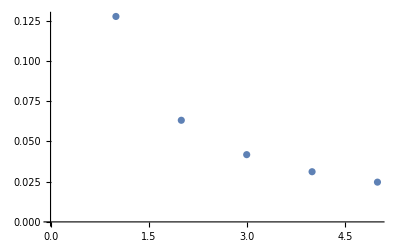

```mathematica
Show[ListPlot[Total[results,{2, 3}]/numsamples^2],ListPlot[Table[5000/x^1.6 + 20, {x, {10, 20, 30, 40, 50}} ], PlotStyle->Red]]
```

```mathematica
Total[results,{2, 3}]/numsamples^2
```

{0.127605,0.0631255,0.0417682,0.0311669,0.0246943}

```mathematica
$MaxLicenseSubprocesses
```

16

```mathematica
Pj[Ps_, j_, k_, l_] :=   Module[{list= Ps,a},a=Length[list];
rtn = PauliMatrix[4];
rtn2 = PauliMatrix[4];
For[i=1,i<a + 1,i++,rtn=list[[i]].rtn;
rtn2 = list[[i]].rtn2;
If[ i == l, rtn2 = PauliMatrix[3].rtn2];
If[ i == k, rtn2 = PauliMatrix[3].rtn2];
If[ i == j, rtn = PauliMatrix[3].rtn];
If[ i == l - a, rtn = PauliMatrix[3].rtn]];
plus.Dagger[rtn2].rtn.Transpose[plus]]
```

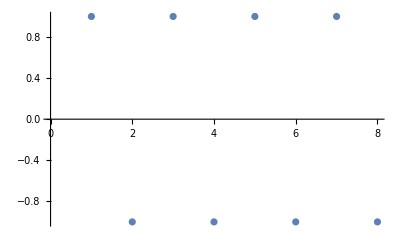

```mathematica
Ps = {P2, PauliMatrix[2],PauliMatrix[2],PauliMatrix[2]};
(*Ps = {PauliMatrix[1],PauliMatrix[1],PauliMatrix[1],PauliMatrix[1]} *)
ListPlot[Table[Pj[Ps, 1, 0,i][[1]][[1]], {i, 1, 2*Length[Ps]}]]
```

```mathematica
Pj[Ps, 2][[1]][[1]]
```

{{0,1},{1,0}}

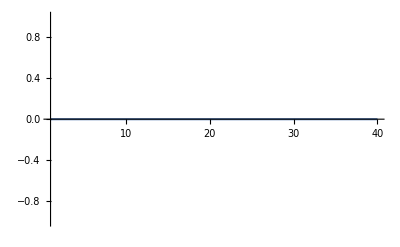

```mathematica
Plot[Sum[Sum[1/Length[Ps]*Cos[α*i/Length[Ps]]*Pj[Ps,i, j, 1], {i, 1, 2*Length[Ps]}], {j, 1, Length[Ps]}], {α, 1, 40}] (* Interesting *)
```

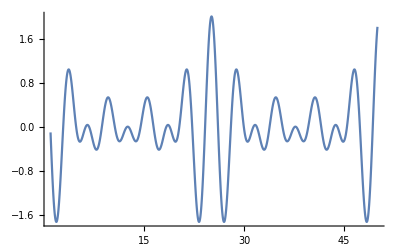

```mathematica
Plot[Sum[Sum[Sum[1/Length[Ps]*Cos[α*i/Length[Ps]]*Pj[Ps,i ,j, k], {i, 1, 2*Length[Ps]}], {j, 1, k}], {k, 1, Length[Ps]}], {α,1, 50}]
```

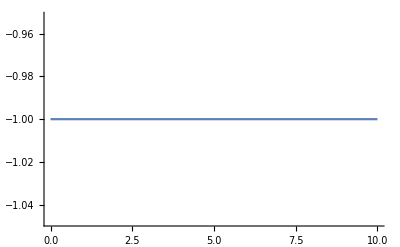

```mathematica
Ps = {PauliMatrix[2],PauliMatrix[2],PauliMatrix[2]};
Plot[Vij[Ps, 1, 2], {ω, 0, 10}]
```

```mathematica
Zj[1,Ps]
```

{{1,0},{0,1}}

```mathematica
Ps = {P4, P8, PauliMatrix[4], MatrixExp[-ⅈ*PauliMatrix[3]*π/4], P4,PauliMatrix[4], P4};
```

```mathematica
Table[Pj[Ps, 1, 2,i][[1]][[1]], {i, 1, 2*Length[Ps]}]//N
```

{-0.382683+5.88785×10^-17 ⅈ,-0.707107+3.92523×10^-17 ⅈ,-0.707107+3.92523×10^-17 ⅈ,-0.707107+3.92523×10^-17 ⅈ,-0.5-0.270598 ⅈ,-0.5-0.270598 ⅈ,1.96262×10^-16-0.382683 ⅈ,-0.92388+1.96262×10^-17 ⅈ,-0.707107-1.96262×10^-17 ⅈ,-0.707107-1.96262×10^-17 ⅈ,-0.707107-3.92523×10^-17 ⅈ,-0.5-0.270598 ⅈ,-0.5-0.270598 ⅈ,1.96262×10^-16-0.382683 ⅈ}